# Mosquito population dynamics include Early instars, layter instars, pupae, and adults female.

## How to use

Using the code here we can determine seasonal patterns in infection and test the effect of IRS on the mosquito populations. This is a deterministic implementation of the model by White et al. 2011, which itself relies on other references and particularly Griffin et al. 2010. The workflow is to feed the function here the seasonal and or IRS scheme that we want and to take the output and feed it to the parameter file of the ABM. The final vector should be normalized by the predicted abundance without an intervention, to get the amplitude to multiply the biting rate parameter in the model.

White MT, Griffin JT, Churcher TS, Ferguson NM, Basáñez M-G, Ghani AC. Modelling the impact of vector control interventions on Anopheles gambiae population dynamics. Parasit Vectors. 2011;4: 153.

```mathematica
ClearAll[A,P,L,M,K,f,MuM,MuE,MuL, c, TimeMax];
```

## Carrying capacity

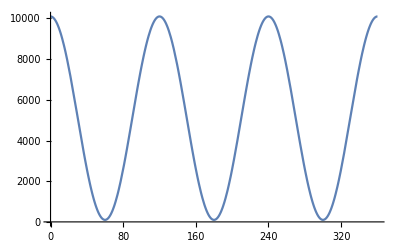

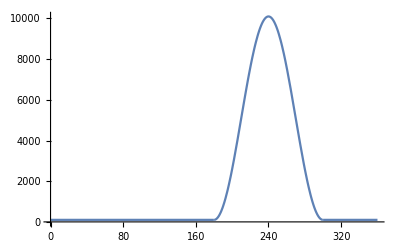

```mathematica
K[t_]:=10000*(0.5+0.5*Sin[2π*(t/120+30/120)])+100; (* Carrying capacity is just a sin function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. the 10000 is just an arbitrary number. Carrying capacity is just for the first 2 stages, as their mortality rates depend on carrying capacity *)
f[t_]:=Piecewise[{{K[t],180<Mod[t,360]<300}},100];  (*Seasonality in carrying capacity. In the rainy season (days 180 to 300, calculate K. Otherwise set to a baseline of 100*)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

## Mortality rates

### Non - adult mortality rates

```mathematica
(* MuE and MuL are the daily mortality of eggs+early larvae and of late larva stages, respectively. 
Both are density-dependent on the number of early and late larva stages, calculated as (A+L)/f, where f is the environmental carrying capacity at time t; 
\mu_E^0 and \mu_L^0 are assumed to be 0.035 and γ = 13.25. These values are taken from Table 1.
The equations are Eq. 7 in the paper.
*)
```

```mathematica
MuE[t_]:=0.035*(1+(A[t]+L[t])/f[t]); 
MuL[t_]:=0.035*(1+13.25*(A[t]+L[t])/f[t]);
```

### Adult mortality rates -- this is the definition of the intervention

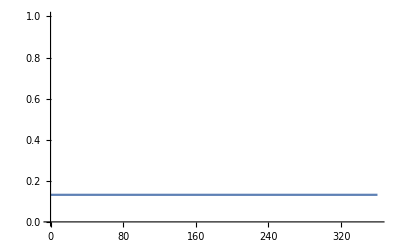

0.8

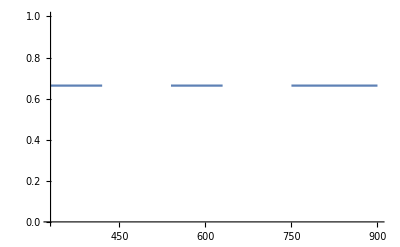

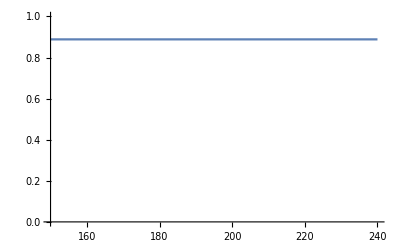

```mathematica
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)

(*MuM is the daily mortality rate of adult mosquitos.The Log turns the w into a rate.*)

(* Example 0: No external mortality rates (no IRS), so c=0 *)
c=0;
TimeMax=360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= {-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,0<t<TimeMax};
Plot[Evaluate[MuM[0,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]

(* Example 1: Our Ghana data. Assume c=0.8 *)
c=0.8
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,330<t<420||540<t<630||750<t<900}},MuM0]; (* The part of 330<t<420||540<t<630||750<t<900 is the IRS scheme of our Ghana data. *)
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,1000},PlotRange->{0,1}]


(* Example 2: IRS of 3 months, May-July, with c=0.9 *)
c=0.9;
TimeMax=360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,150<t<240}},MuM0];
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]
(* Plot the mortality rates *)
```

## Mosquito population dynamics without IRS (only seasonality)

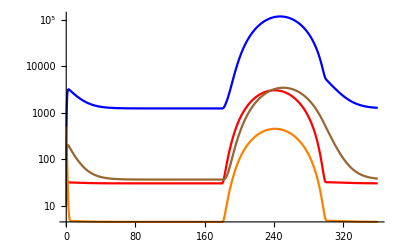

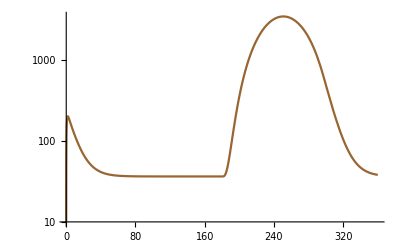

```mathematica
(* When there is no IRS then the mortality rate of adults is just the basline MuM0. This goes in the calculation of M'[t] *)

β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM0*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
MosquitoNoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];
```

## Mosquito population dynamics with IRS

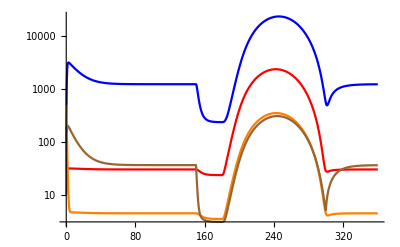

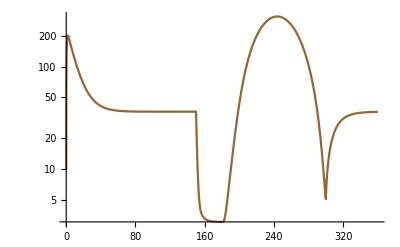

```mathematica
(* Need to set the IRS scheme, so change these next three lines as necessary *)
TimeMax=360;
c=0.9;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,150<t<300}},MuM0];

β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[c,0.92,0.97,0.207,0.86,t]*M[t], (*Adult mosquitos, half of them are female*)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown}] (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];(* Obtain mosquito abundance with intervention*)
```

## Export to a file

{0.1805,0.0768647}

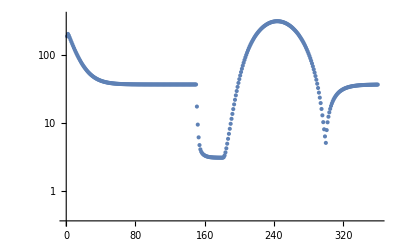

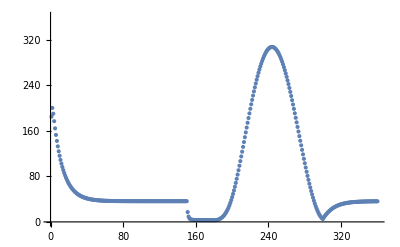

```mathematica
(* MosquitoAbundaceNormalized=MosquitoIRS/MosquitoNoIRS;  *)
data=Transpose@{Range[0,TimeMax],Flatten[MosquitoIRS,2]};
data=Delete[data,1];
Mean[data*0.001]
ListLogPlot[data, PlotRange->{0,Max[data]+1}]
ListPlot[data, PlotRange->{0,Max[data]+1}]
```

```mathematica
Export["~/Documents/malaria_interventions/mosquito_population_IRS02.csv",data];
```

```mathematica
data
```

{{1,184.982},{2,200.255},{3,190.092},{4,176.937},{5,164.343},{6,152.794},{7,142.28},{8,132.722},{9,124.034},{10,116.136},{11,108.956},{12,102.43},{13,96.4955},{14,91.0999},{15,86.1935},{16,81.7316},{17,77.6735},{18,73.9824},{19,70.6246},{20,67.5698},{21,64.7903},{22,62.261},{23,59.9592},{24,57.864},{25,55.9568},{26,54.2205},{27,52.6395},{28,51.1998},{29,49.8887},{30,48.6944},{31,47.6065},{32,46.6153},{33,45.7123},{34,44.8893},{35,44.1394},{36,43.4558},{37,42.8327},{38,42.2648},{39,41.747},{40,41.2748},{41,40.8444},{42,40.4518},{43,40.0938},{44,39.7673},{45,39.4695},{46,39.1979},{47,38.9502},{48,38.7242},{49,38.518},{50,38.3299},{51,38.1583},{52,38.0018},{53,37.8589},{54,37.7286},{55,37.6097},{56,37.5012},{57,37.4022},{58,37.3118},{59,37.2294},{60,37.1541},{61,37.0855},{62,37.0228},{63,36.9656},{64,36.9135},{65,36.8658},{66,36.8224},{67,36.7827},{68,36.7465},{69,36.7135},{70,36.6833},{71,36.6558},{72,36.6307},{73,36.6078},{74,36.5868},{75,36.5677},{76,36.5503},{77,36.5344},{78,36.5199},{79,36.5066},{80,36.4946},{81,36.4835},{82,36.4734},{83,36.4642},{84,36.4559},{85,36.4482},{86,36.4412},{87,36.4348},{88,36.429},{89,36.4237},{90,36.4188},{91,36.4144},{92,36.4104},{93,36.4067},{94,36.4033},{95,36.4002},{96,36.3974},{97,36.3949},{98,36.3925},{99,36.3904},{100,36.3884},{101,36.3867},{102,36.3851},{103,36.3836},{104,36.3822},{105,36.381},{106,36.3799},{107,36.3788},{108,36.3779},{109,36.377},{110,36.3763},{111,36.3755},{112,36.3749},{113,36.3743},{114,36.3738},{115,36.3733},{116,36.3728},{117,36.3724},{118,36.372},{119,36.3717},{120,36.3714},{121,36.3711},{122,36.3708},{123,36.3706},{124,36.3704},{125,36.3702},{126,36.37},{127,36.3698},{128,36.3697},{129,36.3695},{130,36.3694},{131,36.3693},{132,36.3692},{133,36.3691},{134,36.369},{135,36.3689},{136,36.3688},{137,36.3688},{138,36.3687},{139,36.3687},{140,36.3686},{141,36.3686},{142,36.3685},{143,36.3685},{144,36.3685},{145,36.3684},{146,36.3684},{147,36.3684},{148,36.3683},{149,36.3683},{150,36.3683},{151,17.2685},{152,9.39143},{153,6.1095},{154,4.70717},{155,4.07478},{156,3.76073},{157,3.5824},{158,3.46624},{159,3.38242},{160,3.31829},{161,3.26789},{162,3.22788},{163,3.19605},{164,3.17072},{165,3.1506},{166,3.13461},{167,3.12193},{168,3.11187},{169,3.1039},{170,3.09758},{171,3.09257},{172,3.08861},{173,3.08546},{174,3.08297},{175,3.081},{176,3.07943},{177,3.07819},{178,3.07721},{179,3.07643},{180,3.07582},{181,3.07874},{182,3.13264},{183,3.31888},{184,3.67987},{185,4.21967},{186,4.93158},{187,5.81542},{188,6.88234},{189,8.15307},{190,9.65455},{191,11.4171},{192,13.4722},{193,15.8511},{194,18.5834},{195,21.6962},{196,25.2119},{197,29.1483},{198,33.5167},{199,38.3213},{200,43.5594},{201,49.2211},{202,55.2897},{203,61.7427},{204,68.5526},{205,75.6883},{206,83.1159},{207,90.8},{208,98.7044},{209,106.793},{210,115.031},{211,123.383},{212,131.818},{213,140.302},{214,148.808},{215,157.304},{216,165.766},{217,174.166},{218,182.48},{219,190.684},{220,198.756},{221,206.673},{222,214.415},{223,221.961},{224,229.291},{225,236.388},{226,243.232},{227,249.807},{228,256.095},{229,262.081},{230,267.75},{231,273.088},{232,278.08},{233,282.715},{234,286.981},{235,290.866},{236,294.362},{237,297.459},{238,300.15},{239,302.427},{240,304.287},{241,536.432},{242,751.177},{243,955.366},{244,1152.28},{245,1341.18},{246,1519.9},{247,1686.59},{248,1840.12},{249,1980.01},{250,2106.22},{251,2218.98},{252,2318.68},{253,2405.82},{254,2480.93},{255,2544.58},{256,2597.32},{257,2639.71},{258,2672.29},{259,2695.58},{260,2710.1},{261,2716.34},{262,2714.77},{263,2705.84},{264,2690.01},{265,2667.69},{266,2639.3},{267,2605.25},{268,2565.92},{269,2521.69},{270,2472.94},{271,2420.04},{272,2363.32},{273,2303.15},{274,2239.87},{275,2173.8},{276,2105.28},{277,2034.63},{278,1962.17},{279,1888.21},{280,1813.05},{281,1737.01},{282,1660.36},{283,1583.41},{284,1506.44},{285,1429.73},{286,1353.54},{287,1278.15},{288,1203.82},{289,1130.8},{290,1059.34},{291,989.671},{292,922.032},{293,856.648},{294,793.733},{295,733.499},{296,676.145},{297,621.865},{298,570.843},{299,523.252},{300,479.255},{301,438.98},{302,402.328},{303,369.018},{304,338.752},{305,311.254},{306,286.268},{307,263.567},{308,242.939},{309,224.196},{310,207.165},{311,191.688},{312,177.624},{313,164.843},{314,153.228},{315,142.672},{316,133.077},{317,124.357},{318,116.429},{319,109.223},{320,102.672},{321,96.7161},{322,91.3005},{323,86.3759},{324,81.8975},{325,77.8244},{326,74.1196},{327,70.7495},{328,67.6834},{329,64.8937},{330,62.3551},{331,60.0448},{332,57.942},{333,56.0278},{334,54.2851},{335,52.6983},{336,51.2534},{337,49.9375},{338,48.7388},{339,47.647},{340,46.6522},{341,45.7459},{342,44.9199},{343,44.1673},{344,43.4813},{345,42.8559},{346,42.2859},{347,41.7662},{348,41.2924},{349,40.8604},{350,40.4664},{351,40.1071},{352,39.7795},{353,39.4806},{354,39.208},{355,38.9594},{356,38.7326},{357,38.5257},{358,38.3369},{359,38.1647},{360,38.0076}}